```mathematica
Eff=Import[NotebookDirectory[]<>"../calc/efficencies.txt","Table"];
Eff//MatrixForm
EffErr=Import[NotebookDirectory[]<>"../calc/efficencies_error.txt","Table"];
EffErr//MatrixForm
```

(0.391474 | 0.000011 | 0.004406 | 0.00001
0.00016 | 0.890762 | 0.003585 | 0.
0.01259 | 0.031002 | 0.848524 | 0.000457
0. | 0. | 0.001868 | 0.966965)

(0.001594 | 0.000011 | 0.000235 | 0.00001
0.000041 | 0.001015 | 0.000212 | 0.
0.000364 | 0.000564 | 0.001274 | 0.000068
0. | 0. | 0.000153 | 0.000569)

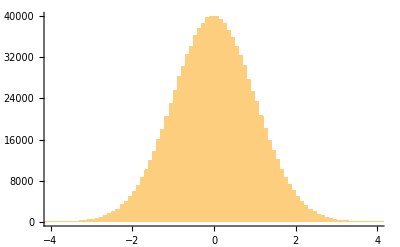

```mathematica
rns=Table[Table[RandomVariate[NormalDistribution[]],{j,1,4},{k,1,4}],{i,1,1000000}];
Histogram[rns[[All,1,1]],100,PlotRange->{{-4,4},All}]
```

```mathematica
NoisyInvEff=Inverse[Eff+EffErr*#]&/@rns;
```

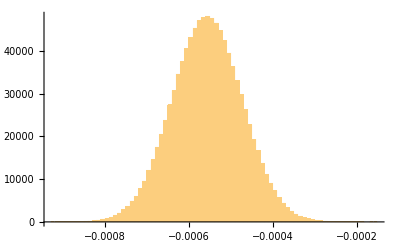

```mathematica
Histogram[NoisyInvEff[[All,3,4]],100,PlotRange->{All,All}]
```

```mathematica
NoisyInvEffSort=Table[NoisyInvEff[[All,i,j]],{i,1,4},{j,1,4}];
Inverse[Eff]
A=Mean[#]&/@#&/@NoisyInvEffSort;
A//MatrixForm
EffErr//MatrixForm
sA=StandardDeviation[#]&/@#&/@NoisyInvEffSort;
sA//MatrixForm
```

{{2.55487,0.000430231,-0.0132681,-0.0000201509},{-0.000306389,1.1228,-0.00474222,2.2444×10^-6},{-0.0378969,-0.0410295,1.17889,-0.000556766},{0.0000732098,0.0000792614,-0.0022774,1.03416}}

(2.55492 | 0.000430274 | -0.0132686 | -0.0000201066
-0.0003061 | 1.1228 | -0.00474228 | 2.24399×10^-6
-0.0378974 | -0.0410288 | 1.17889 | -0.000556658
0.0000732002 | 0.000079248 | -0.00227706 | 1.03417)

(0.001594 | 0.000011 | 0.000235 | 0.00001
0.000041 | 0.001015 | 0.000212 | 0.
0.000364 | 0.000564 | 0.001274 | 0.000068
0. | 0. | 0.000153 | 0.000569)

(0.0103942 | 0.0000409682 | 0.000710507 | 0.0000264055
0.000118037 | 0.00127951 | 0.000280685 | 3.59355×10^-7
0.00110858 | 0.000751255 | 0.00177081 | 0.0000828575
6.36948×10^-6 | 6.64706×10^-6 | 0.000186439 | 0.000608553)

```mathematica
Round[Eff.A,10^-4]//MatrixForm
AccountingForm[MatrixForm[sA],2]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0.01 | 0.000041 | 0.00071 | 0.000026
0.00012 | 0.0013 | 0.00028 | 0.00000036
0.0011 | 0.00075 | 0.0018 | 0.000083
0.0000064 | 0.0000066 | 0.00019 | 0.00061)

```mathematica
Export[NotebookDirectory[]<>"../calc/invEfficencies_Math.txt",A,"Table"];
sAexp=SetPrecision[sA,2];
Export[NotebookDirectory[]<>"../calc/invEfficencies_error_Math.txt",ToString[AccountingForm[#,2]]&/@#&/@sA,"Table"];
```

```mathematica
Quiet[100EffErr/Eff]//MatrixForm
Abs[100sA/Inverse[Eff]]//MatrixForm
```

(0.407179 | 100. | 5.33364 | 100.
25.625 | 0.113947 | 5.91353 | Indeterminate
2.89118 | 1.81924 | 0.150143 | 14.8796
Indeterminate | Indeterminate | 8.19058 | 0.0588439)

(0.406837 | 9.52239 | 5.35501 | 131.039
38.5251 | 0.113957 | 5.91885 | 16.0112
2.92525 | 1.83101 | 0.15021 | 14.8819
8.70031 | 8.38625 | 8.1865 | 0.0588449)